# Projekt

## Czas życia dowolnego systemu bez napraw

Przedstawmy nasz system jako graf zorientowany gdzie każdy wierzchołek odpowiada komponentowi.

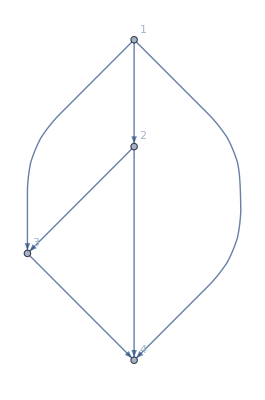

```mathematica
systemGraph=Graph[{1->2,1->3,1->4,2->3,2->4,3->4},VertexLabels->"Name"]
```

Zdefiniujmy minimalną ścieżkę  jako ścieżkę między początkiem a końcem naszego systemu, taką że wszystkie komponenty w tej ścieżce muszą działać żeby system działał, ale jeśli jakikolwiek komponent w naszej ścieżce nie działa to system też nie działa. Nasz system ma następujące minimalne ścieżki:

```mathematica
rowMinimalPaths=FindPath[systemGraph,1,4,Infinity,All]
```

{{1,4},{1,3,4},{1,2,4},{1,2,3,4}}

Niech xi informuje że czy dany komponent działa. Dokładnie xi=1 jeśli i-ty komponent działa i 0 jeśli nie działa. 
Następnie zdefinijmy wektor stanu naszego systemu jako x=(x1,..xn) 
Zdefniniujmy funkcje strukturalną Φ(x) (tłumaczenie?) wektora stanu x. Funkcja strukturalna równa się 1 jeśli system działa dla danego wektora stanu i 0 jeśli system nie działa.
strona 580 

Znajdźmy teraz funkcję strukturalną Φ naszego systemu. Wiemy, że można ją uzyskać z wiedzy o minimalnych ścieżkach używając wzoru (strona 583)

Φ(x)=1-∏_A_j^□ (1-∏_(i∈A_j)^□ x_(i□))

gdzie Aj to to minimalna ścieżka

```mathematica
computeStructureFunction[systemGraph_,systemSource_,systemSink_]:=Module[{rowMinimalPaths,minimalPaths,stateVector,replaceVertexNumbersWithComponentState,pathStates,structureFunction},

replaceVertexNumbersWithComponentState[path_,stateVector_]:= stateVector[[#]]&/@path;

stateVector=Table[x[i],{i,VertexCount[systemGraph]}];
rowMinimalPaths=FindPath[systemGraph,systemSource,systemSink,Infinity,All];
minimalPaths=replaceVertexNumbersWithComponentState[#,stateVector]&/@rowMinimalPaths;
pathStates=Apply[Times,minimalPaths,{1}];
structureFunction=1-Apply[Times,1-pathStates];
structureFunction
](*todo duże litery*)

structureFunction=computeStructureFunction[systemGraph,1,4]
```

1-(1-x[1] x[4]) (1-x[1] x[2] x[4]) (1-x[1] x[3] x[4]) (1-x[1] x[2] x[3] x[4])

zdefiniujmy funkcję niezawodności jako:

r(p)=P(Φ(x)=1) gdzie p=(p_1,...,p_n) to wektor prawdopodobieństw działania poszczególnych komponentów

```mathematica
computeReliabilityFunction[structureFunction_]:=Module[{reliabilityFunction},
Clear[p];
reliabilityFunction=Expand[structureFunction]/.a_^p_:>a ;(*Ponieważ x[i] ma rozkład bernouliego to x[i]^j=x[i]*)
reliabilityFunction/.x->p
]

reliabilityFunction=computeReliabilityFunction[structureFunction]
```

p[1] p[4]

Ma sens, tylko komponenty 1 i 4 mają znaczenie: muszą oba działać żeby system działał. 

Zdefiniujmy funkcje przeżycia jako F_s1=P(czas życia systemu>t)=1-F(t) gdzie F(t) to dystrybuanta. Funkcja przeżycia całego systemu jest dana wzorem r(F_s1,...,F_s2) (strona 603)
Załóżmy teraz, że czas życia wszystkich komponentów ma rozkład wykładniczy

(1-(Piecewise[{{1-ⅇ^(-0.2 t), t≥0}, {0, True}}]))^2

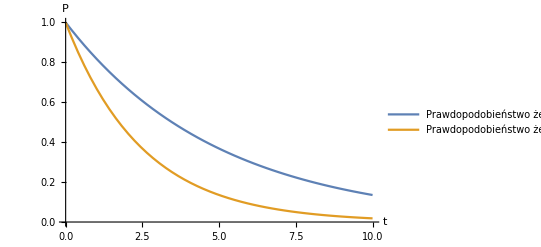

```mathematica
intensity=0.2;
exponentialSurvivalFunction=1-CDF[ExponentialDistribution[intensity],t];
componentsSurvivalFunctions=Table[exponentialSurvivalFunction,VertexCount[systemGraph]];

ComputeSurvivalFunction[componentsSurvivalFunctions_,reliabilityFunction_]:=Module[{systemSurvivalFunction,systemLifeTimePDF},
For[i=1,i<=Length[componentsSurvivalFunctions],i++,p[i]=componentsSurvivalFunctions[[i]]];
systemSurvivalFunction=Evaluate[reliabilityFunction];
systemSurvivalFunction
] ;

systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{exponentialSurvivalFunction,systemSurvivalFunction},{t,0,10},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że czas życia jednego komponentu jest większy niż t","Prawdopodobieństwo że czas życia całego systemu jest większy niż t"}]
```

System z naprawami

Zakładamy, że początkowo wszystkie komponenty działają. Czas działania komponentu ma rozkład wykładniczy z intensywnością λ, a czas naprawy komponentu ma rozkład wykładniczy z intensywnością μ. 
Zdefiniujmy funkcję dyspozycyjności jako 

A(t)=P{system działa w chwili t}

A(t)=r(A_i(t)....A_n(t))     gdzie A_i(t)=P{komponent i-ty działa w chwili t}

A_i(t)=P_00(t)=μ_i/(μ_i+λ_i)+λ_i/(μ_i+λ_i)ⅇ^(-(μ_i+λ_i)t)

Kontynuacja poprzedniego przykładu

2 (0.333333+0.666667 ⅇ^(-0.3 t))^3-(0.333333+0.666667 ⅇ^(-0.3 t))^4

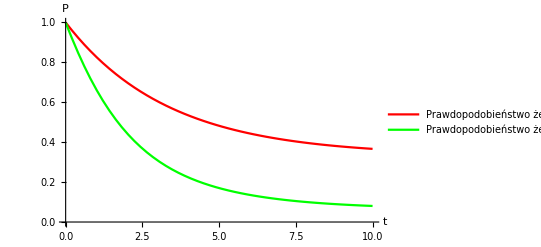

```mathematica
intensityFunctioning=0.2;
intensityRepairing=0.1;

exponentialAvailabilityFunction[t_]=intensityRepairing/(intensityFunctioning+intensityRepairing)+intensityFunctioning/(intensityFunctioning+intensityRepairing)*ⅇ^(-(intensityFunctioning+intensityRepairing)*t);
componentsAvailabilityFunctions=Table[exponentialAvailabilityFunction[t],VertexCount[systemGraph]];

reliabilityFunction=computeReliabilityFunction[structureFunction];

ComputeAvailabilityFunction[componentsAvailabilityFunctions_,reliabilityFunction_]:=Module[{systemAvailabilityFunction},
Clear[p];

For[i=1,i<=Length[componentsAvailabilityFunctions],i++,p[i]=componentsAvailabilityFunctions[[i]]];
systemAvailabilityFunction[t]=Evaluate[reliabilityFunction];
systemAvailabilityFunction[t]
] ;


systemAvailabilityFunction=ComputeAvailabilityFunction[componentsAvailabilityFunctions,reliabilityFunction]

Plot[{exponentialAvailabilityFunction[t],systemAvailabilityFunction},{t,0,10},PlotStyle->{Red,Green},AxesLabel->{t,P},AxesOrigin->{0,0},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że czas działania bez awarii jednego komponentu jest większy niż t","Prawdopodobieństwo że czas działania całego systemu bez awarii jest większy niż t"}](*todo oś x nie w 0, zły opis funkcji, może coś o asymptotach*)
```

Weźmy inny system.

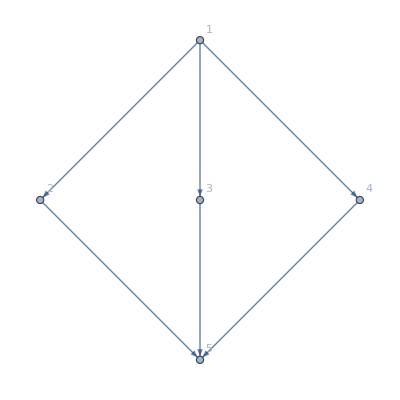

1-(1-x[1] x[2] x[5]) (1-x[1] x[3] x[5]) (1-x[1] x[4] x[5])

p[1] p[2] p[5]+p[1] p[3] p[5]-p[1] p[2] p[3] p[5]+p[1] p[4] p[5]-p[1] p[2] p[4] p[5]-p[1] p[3] p[4] p[5]+p[1] p[2] p[3] p[4] p[5]

3 (1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^3-3 (1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^4+(1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^5

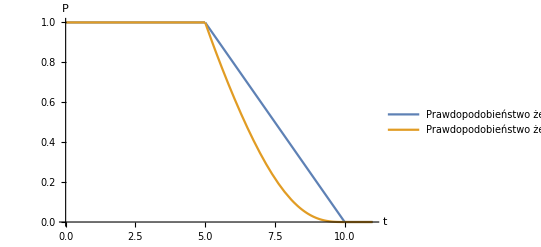

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,1->4,2->5,3->5,4->5},VertexLabels->"Name"]
structureFunction=computeStructureFunction[systemGraph,1,5]
reliabilityFunction=computeReliabilityFunction[structureFunction]

uniformSurvivalFunction=1-CDF[UniformDistribution[{5,10}],t];
componentsSurvivalFunctions=Table[uniformSurvivalFunction,VertexCount[systemGraph]];

systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{uniformSurvivalFunction,systemSurvivalFunction},{t,0,11},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że czas życia jednego komponentu jest większy niż t","Prawdopodobieństwo że czas życia całego systemu jest większy niż t"}]
```

```mathematica
(*Sprawdzenie z książką strona 588 przykład 9.15*)
Expand[p1*p5*(1-(1-p2)*(1-p3)*(1-p4))]
```

p1 p2 p5+p1 p3 p5-p1 p2 p3 p5+p1 p4 p5-p1 p2 p4 p5-p1 p3 p4 p5+p1 p2 p3 p4 p5

Inne przykład

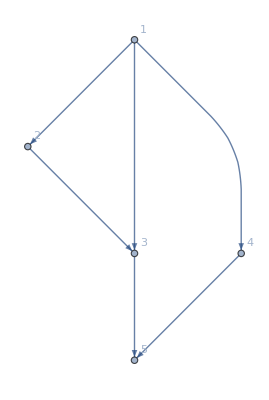

1-(1-x[1] x[3] x[5]) (1-x[1] x[2] x[3] x[5]) (1-x[1] x[4] x[5])

p[1] p[3] p[5]+p[1] p[4] p[5]-p[1] p[3] p[4] p[5]

2 (1-(Piecewise[{{1-ⅇ^(-0.3 t), t≥0}, {0, True}}]))^3-(1-(Piecewise[{{1-ⅇ^(-0.3 t), t≥0}, {0, True}}]))^4

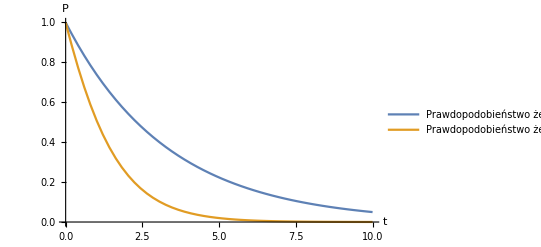

2 (0.25+0.75 ⅇ^(-0.4 t))^3-(0.25+0.75 ⅇ^(-0.4 t))^4

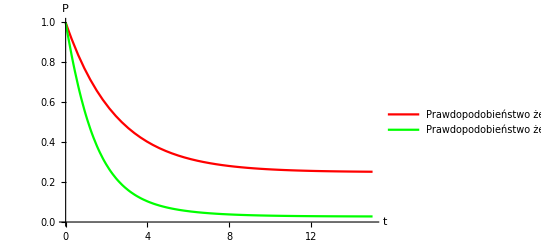

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,1->4,2->3,3->5,4->5},VertexLabels->"Name"]

structureFunction=computeStructureFunction[systemGraph,1,5]
reliabilityFunction=computeReliabilityFunction[structureFunction]

intensityFunctioning=0.3;
intensityRepairing=0.1;

exponentialSurvivalFunction=1-CDF[ExponentialDistribution[intensityFunctioning],t];
componentsSurvivalFunctions=Table[exponentialSurvivalFunction,VertexCount[systemGraph]];
systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{exponentialSurvivalFunction,systemSurvivalFunction},{t,0,10},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że czas życia jednego komponentu jest większy niż t","Prawdopodobieństwo że czas życia całego systemu jest większy niż t"}]

reliabilityFunction=computeReliabilityFunction[structureFunction];(*todo duplikacja*)

exponentialAvailabilityFunction[t_]=intensityRepairing/(intensityFunctioning+intensityRepairing)+intensityFunctioning/(intensityFunctioning+intensityRepairing)*ⅇ^(-(intensityFunctioning+intensityRepairing)*t);(*todo t i duplikacja definicji*)
componentsAvailabilityFunctions=Table[exponentialAvailabilityFunction[t],VertexCount[systemGraph]];

componentsAvailabilityFunctions=Table[exponentialAvailabilityFunction[t],VertexCount[systemGraph]];(*todo duplikacja*)

systemAvailabilityFunction=ComputeAvailabilityFunction[componentsAvailabilityFunctions,reliabilityFunction]
Plot[{exponentialAvailabilityFunction[t],systemAvailabilityFunction},{t,0,15},PlotStyle->{Red,Green},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że czas działania bez awarii jednego komponentu jest większy niż t","Prawdopodobieństwo że czas działania całego systemu bez awarii jest większy niż t"}] (*todo jak wyżej*)
```